# δB nets

## Utilities

```mathematica
ActivationPlot[f_,contours_:Automatic]:=ContourPlot[f[x,y],{x,0,1},{y,0,1},FrameLabel->{x,y},PlotLegends->BarLegend[{Automatic,{0,1}}],PlotRange->All,ColorFunction->(If[#>1/2,Lighter[Red,#],Lighter[Gray,#]]&),ColorFunctionScaling->False,Contours->contours]
```

```mathematica
MarginPacking[]:=Manipulate[
Block[{m,eps,thresholdLine,marginLine,representativeLine,augmentation},
m=Min[x,y];
eps=0.01;
augmentation=Mean[{x,y}]Abs[m-1/2];
thresholdLine=Line[{{1/2,-1},{1/2,1}}];
marginLine={Line[{{m,0.2},{1/2,0.2}}],Text[Style["margin",Bold,FontFamily->"Helvetica"],{m+(1/2-m)/2,0.3}]};
representativeLine={Line[{{m,-0.8},{m,1}}],Text[Style["representative bit",Bold,FontFamily->"Helvetica"],{m,-0.9}]};
Labeled[Plot[
{
Callout[If[m<=1/2,
If[x>=(m+augmentation-eps)&&x<=(m+augmentation+eps),1,Nothing],
If[x>=(1/2+augmentation-eps)&&x<=(1/2+augmentation+eps),1,Nothing]
],Style["augmented bit",Bold,FontColor->Gray],{If[m>1/2,1/2+augmentation,m+augmentation],1.2},CalloutStyle->{Gray},Background->Transparent],
If[m<=1/2,
If[x>m && x<=(m+augmentation),1,Nothing],
If[x>1/2&&x<(1/2+augmentation),1,Nothing]
]
},
{x,0,1},
PlotRange->{{If[m>1/2,0.45,0],If[m>1/2,1,0.55]},{-1,1}},
PlotStyle->Transparent,
Filling->{1->1,2->-0.8},
FillingStyle->LightGray,
Axes->{True,False},
Ticks->{True,False},
Epilog->{Directive[Black],representativeLine,Directive[Gray,Dashed],thresholdLine,marginLine},
ImagePadding->{{0,0},{0,30}},
AspectRatio->2/3
],If[m>1/2,Style["high margin",FontFamily->"Helvetica"],Style["low margin",FontFamily->"Helvetica"]],Bottom]
],{x,0,1},{y,0,1}
]
```

```mathematica
MarginPack[representativeBit_,x_List]:=Module[{μ=Mean[x],δ},
δ=μ Sqrt[(representativeBit-1/2)^2];
If[representativeBit>1/2,Evaluate[1/2+δ],Evaluate[representativeBit+δ]]
]
```

```mathematica
GradientRich[f_,x_List]:=ForAll[x,And[Or[0<=#<1/2,1/2<#<=1]&/@x],And@@(D[f@@x,#]!=0&/@x)]
```

```mathematica
HardEquivalent[f_,g_,x_List]:=ForAll[x,And[Or[0<=#<1/2,1/2<#<=1]&/@x],Harden[f@@x]==g@@Harden[x]]
```

## Repo

## github.com/Z80coder/db-nets

## Paper

## slack channel #db-nets

## Hard equivalence

## Hardening

```mathematica
Harden[x_]:=If[x>1/2,True,False]
Harden[x_List]:=Harden/@x
```

```mathematica
Harden[{0.2,0.6,0.45}]
```

{False,True,False}

## Equivalence condition

∀_(x_i, 0 <= x_i <1/2 ∨ 1/2< x_i <=1)harden(f(x))=g(harden(x))

## E.g. Product logic

```mathematica
ProductAnd[x_,y_]:=x y
```

```mathematica
inputs={{1,1},{1,0},{0,1},{0,0}};
```

```mathematica
And@@#&/@Harden[inputs]
```

{True,False,False,False}

```mathematica
Harden[ProductAnd@@#&/@inputs]
```

{True,False,False,False}

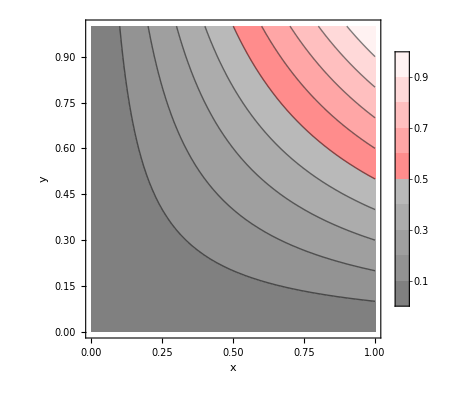

```mathematica
ActivationPlot[ProductAnd]
```

```mathematica
HardEquivalent[ProductAnd,And,{x,y}]
```

∀_({x,y},(0≤x<1/2||1/2<x≤1)&&(0≤y<1/2||1/2<y≤1))If[x y>1/2,True,False]==(If[x>1/2,True,False]&&If[y>1/2,True,False])

```mathematica
Resolve[%,Reals]
```

False

## Gradient-richness

## Richness condition

∀_(x_i, 0 <= x_i <1/2∨1/2 < x_i <=1)(∂f(x))/(∂x_i)!=0

## E.g. Godel logic

```mathematica
GodelAnd[x_,y_]:=Min[x,y]
```

```mathematica
Harden[GodelAnd@@#&/@inputs]
```

{True,False,False,False}

```mathematica
HardEquivalent[GodelAnd,And,{x,y}]
```

∀_({x,y},(0≤x<1/2||1/2<x≤1)&&(0≤y<1/2||1/2<y≤1))If[Min[x,y]>1/2,True,False]==(If[x>1/2,True,False]&&If[y>1/2,True,False])

```mathematica
Resolve[%,Reals]
```

True

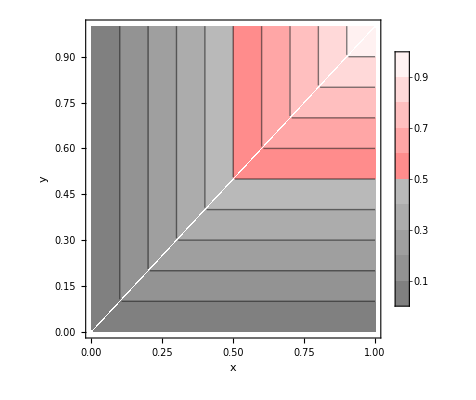

```mathematica
ActivationPlot[GodelAnd]
```

```mathematica
GradientRich[GodelAnd,{x,y}]
```

∀_({x,y},(0≤x<1/2||1/2<x≤1)&&(0≤y<1/2||1/2<y≤1))((Piecewise[{{1, x-y≤0}, {0, True}}])≠0&&(Piecewise[{{0, x-y≤0}, {1, True}}])≠0)

```mathematica
Resolve[%,Reals]
```

False

## Learning to negate

```mathematica
DNegate[w_,x_]:=1-w+x(2w-1)
```

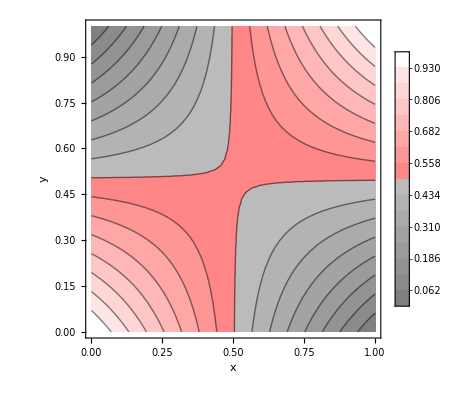

```mathematica
ActivationPlot[DNegate,15]
```

```mathematica
HardEquivalent[DNegate,Function[{x,y},Not[Xor[x,y]]],{x,y}]
```

∀_({x,y},(0≤x<1/2||1/2<x≤1)&&(0≤y<1/2||1/2<y≤1))If[1-x+(-1+2 x) y>1/2,True,False]==!(If[x>1/2,True,False]⊻If[y>1/2,True,False])

```mathematica
Resolve[%,Reals]
```

True

```mathematica
GradientRich[DNegate,{x,y}]
```

∀_({x,y},(0≤x<1/2||1/2<x≤1)&&(0≤y<1/2||1/2<y≤1))(-1+2 y≠0&&-1+2 x≠0)

```mathematica
Resolve[%,Reals]
```

True

## Margin packing

Min[x, y] is a “representative bit” because it’s hard-equivalent to x ∧ y. But Min[x, y] is not gradient-rich.

```mathematica
MarginPacking[]
```

## ∂_∧

```mathematica
DAnd[x_,y_]:=MarginPack[Min[x,y],{x,y}]
```

```mathematica
DAnd[x,y]//PiecewiseExpand
```

Piecewise[{{1/4 (2+x √((-1+2 x)^2)+√((-1+2 x)^2) y), x>1/2&&y>1/2&&x-y≤0}, {1/4 (4 x+x √((-1+2 x)^2)+√((-1+2 x)^2) y), (x≤1/2&&x-y≤0)||(x-y≤0&&y≤1/2)}, {1/4 (2+x √((-1+2 y)^2)+y √((-1+2 y)^2)), x>1/2&&y>1/2&&x-y>0}, {1/4 (4 y+x √((-1+2 y)^2)+y √((-1+2 y)^2)), True}}]

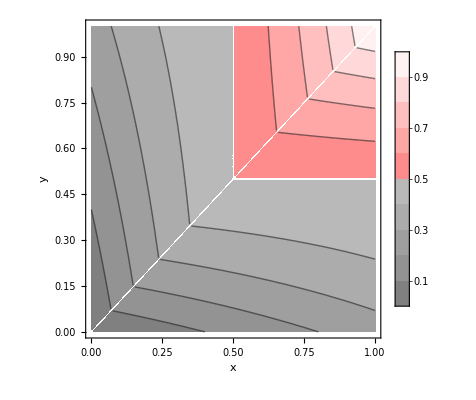

```mathematica
ActivationPlot[DAnd]
```

```mathematica
HardEquivalent[DAnd,Function[{x,y},And[x,y]],{x,y}]
```

∀_({x,y},(0≤x<1/2||1/2<x≤1)&&(0≤y<1/2||1/2<y≤1))If[If[Min[x,y]>1/2,1/2+1/2 (x+y) √((-1/2+Min[x,y])^2),1/2 (x+y) √((-1/2+Min[x,y])^2)+Min[x,y]]>1/2,True,False]==(If[x>1/2,True,False]&&If[y>1/2,True,False])

```mathematica
Resolve[%,Reals]
```

True

```mathematica
GradientRich[DAnd,{x,y}]
```

∀_({x,y},(0≤x<1/2||1/2<x≤1)&&(0≤y<1/2||1/2<y≤1))(If[Min[x,y]>1/2,(((-1/2+Min[x,y]) (Piecewise[{{1, x-y≤0}, {0, True}}])) (x+y))/(√((-1/2+Min[x,y])^2) 2)+1/2 √((-1/2+Min[x,y])^2),(((-1/2+Min[x,y]) (Piecewise[{{1, x-y≤0}, {0, True}}])) (x+y))/(√((-1/2+Min[x,y])^2) 2)+1/2 √((-1/2+Min[x,y])^2)+(Piecewise[{{1, x-y≤0}, {0, True}}])]≠0&&If[Min[x,y]>1/2,(((-1/2+Min[x,y]) (Piecewise[{{0, x-y≤0}, {1, True}}])) (x+y))/(√((-1/2+Min[x,y])^2) 2)+1/2 √((-1/2+Min[x,y])^2),(((-1/2+Min[x,y]) (Piecewise[{{0, x-y≤0}, {1, True}}])) (x+y))/(√((-1/2+Min[x,y])^2) 2)+1/2 √((-1/2+Min[x,y])^2)+(Piecewise[{{0, x-y≤0}, {1, True}}])]≠0)

```mathematica
Resolve[%,Reals]
```

True

## ∂Maj

```mathematica
Majority[True,True,True,False,False]
```

True

```mathematica
MajorityIndex[x_List]:=Ceiling[Length[x]/2]
```

```mathematica
MajorityBit[x_List]:=Sort[x][[MajorityIndex[x]]]
```

```mathematica
DMajority[x_List]:=MarginPack[MajorityBit[x],x]
```

```mathematica
Manipulate[ActivationPlot[Function[{x,y},DMajority[{x,y,z}]]],{z,0,1}]
```

## Toy example

ge(sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((sum((0, not(xor(ne(very-cold, 0), False)))), not(xor(ne(cold, 0), True)))), not(xor(ne(warm, 0), True)))), not(xor(ne(very-warm, 0), True)))), not(xor(ne(outside, 0), True)))), not(xor(ne(very-cold, 0), True)))), not(xor(ne(cold, 0), False)))), not(xor(ne(warm, 0), False)))), not(xor(ne(very-warm, 0), True)))), not(xor(ne(outside, 0), False)))), not(xor(ne(very-cold, 0), False)))), not(xor(ne(cold, 0), False)))), not(xor(ne(warm, 0), True)))), not(xor(ne(very-warm, 0), False)))), not(xor(ne(outside, 0), False)))), not(xor(ne(very-cold, 0), False)))), not(xor(ne(cold, 0), False)))), not(xor(ne(warm, 0), True)))), not(xor(ne(very-warm, 0), False)))), not(xor(ne(outside, 0), False)))), 11)

```mathematica
4 !verycold+4 !cold+(3 warm+!warm)+(verywarm+3!verywarm)+(outside+3 !outside)≥11
```

if
	(not very-cold) and (not cold) and (not outside

)
then
	wear a t-shirt

## Experiments

## Iris dataset

## Noisy XOR

## MNIST

## Summary

- ∂B nets can learn discrete, boolean-valued functions by gradient descent
- Unlike existing approaches

 to neural network binarization, the boolean-valued functions have provably identical accuracy
- ‘Margin packing’ is a potentially general technique for constructing 

differentiable functions that are hard-equivalent yet gradient-rich
- For safety-critical domains: better interpretability, and symbolic verification by SAT solvers
- For edge deployment: 1-bit weights yield small models at inference time
- Performance is already better than many classifiers
- But more work to do: explore space of differentiable nets that are hard-equivalent to discrete functions